# Homework 1

## Problem 2.3

### Graph

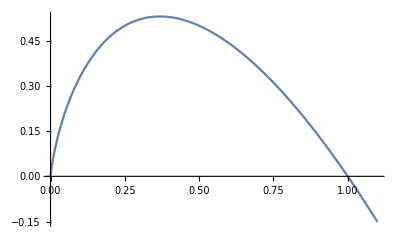

```mathematica
Plot[{-x Log[2,x]},{x,0,1.1}]
```

## Problem 2.24 (b)

### Definitions

Define a simplification function based on 0≤p≤1

```mathematica
FS24b[aa_]:=FullSimplify[aa,Assumptions->{p∈Reals,0≤p≤1}]
```

Define the binary entropy function in terms of base 2 logarithms

```mathematica
H[pp_]:=-pp Log[2,pp]-(1-pp)Log[2,(1-pp)]
H[p]//FS24b
```

((-1+p) Log[1-p]-p Log[p])/Log[2]

Define the binary entropy function in terms of natural logarithms

```mathematica
He[pp_]:=-pp Log[pp]-(1-pp)Log[1-pp]
He[p]//FS24b
```

(-1+p) Log[1-p]-p Log[p]

### Integrate

Using base 2 logarithms

```mathematica
Integrate[H[p],{p,0,1}]//FS24b
Integrate[H[p],{p,0,1}]//FS24b//N
```

1/Log[4]

0.721348

Using natural logarithms

```mathematica
Integrate[He[p],{p,0,1}]//FS24b
Integrate[He[p],{p,0,1}]//FS24b//N
```

1/2

0.5

Checking that changing from nats to bit yields the same result.

```mathematica
(1/2)Log[2,ⅇ]//N
```

0.721348

## Problem 2.24 (c)

### Definitions

Define a simplification function based on 0≤p≤1

```mathematica
FS24c[aa_]:=FullSimplify[aa,Assumptions->{p∈Reals,0≤p≤1,p1∈Reals,0≤p1≤1,p2∈Reals,0≤p2≤1,p3∈Reals,0≤p3≤1,0<p1+p2<1}]
```

Reuse the binary entropy function in terms of base 2 logarithms from part (b)

```mathematica
H[p]//FS24b
```

((-1+p) Log[1-p]-p Log[p])/Log[2]

Reuse the binary entropy function in terms of natural logarithms from part (b)

```mathematica
He[p]//FS24b
```

(-1+p) Log[1-p]-p Log[p]

### Function Creation

```mathematica
H[p1]+H[p2]+H[p3]//FS24c
```

1/Log[2](2 p1 ArcTanh[1-2 p1]+2 p2 ArcTanh[1-2 p2]+2 p3 ArcTanh[1-2 p3]+Log[-1/((-1+p1) (-1+p2) (-1+p3))])

```mathematica
FS24c[(H[p1]+H[p2]+H[p3]/.{p3->(1-p1-p2)})]/.{p3->(1-p1-p2)}//FS24c
```

1/Log[2](2 p1 ArcTanh[1-2 p1]+2 p2 ArcTanh[1-2 p2]+2 (p1+p2) ArcTanh[1-2 p1-2 p2]-Log[-(-1+p1) (-1+p2) (-1+p1+p2)])

```mathematica
FS24c[(H[p1]+H[p2]+H[1-p1-p2])]
```

1/Log[2](2 p1 ArcTanh[1-2 p1]+2 p2 ArcTanh[1-2 p2]+2 (p1+p2) ArcTanh[1-2 p1-2 p2]-Log[-(-1+p1) (-1+p2) (-1+p1+p2)])

```mathematica
FS24c[(H[p1]H[p2]H[1-p1-p2])]
```

1/Log[2]^3((-1+p1) Log[1-p1]-p1 Log[p1]) ((-1+p2) Log[1-p2]-p2 Log[p2]) ((-1+p1+p2) Log[1-p1-p2]-(p1+p2) Log[p1+p2])

```mathematica
p3
```

p3

```mathematica
p2
```

p2

```mathematica
p1
```

p1

```mathematica
H[p1 p2 p3]//FS24c
H[p1 p2 p3]/.{p3->(1-p1-p2)}//FS24c
```

(2 p1 p2 p3 ArcTanh[1-2 p1 p2 p3]-Log[1-p1 p2 p3])/Log[2]

-1/Log[2](2 p1 p2 (-1+p1+p2) ArcTanh[1+2 p1 p2 (-1+p1+p2)]+Log[1+p1 p2 (-1+p1+p2)])

```mathematica
-FS24c[p1 Log[2,p1]+p2 Log[2,p2]+p3 Log[2,p3]+(1-p1-p2-p3)Log[2,(1-p1-p2-p3)]]
-FS24c[p1 Log[2,p1]+p2 Log[2,p2]+p3 Log[2,p3]+(1-p1-p2-p3)Log[2,(1-p1-p2-p3)]]/.{p3->(p1+p2)}//FS24c
```

-1/Log[2](p1 Log[p1]+p2 Log[p2]-(-1+p1+p2+p3) Log[1-p1-p2-p3]+p3 Log[p3])

-1/Log[2](p1 Log[p1]+(1-2 p1-2 p2) Log[1-2 p1-2 p2]+p2 Log[p2]+(p1+p2) Log[p1+p2])

```mathematica
Integrate[Integrate[-FS24c[FS24c[p1 Log[2,p1]+p2 Log[2,p2]+p3 Log[2,p3]+(1-p1-p2-p3)Log[2,(1-p1-p2-p3)]]/.{p3->(p1+p2)}],{p2,p1,1}],{p1,0,1}]//FS24c
```

Undefined

```mathematica
Integrate[FS24c[Integrate[-FS24c[p1 Log[2,p1]+p2 Log[2,p2]+p3 Log[2,p3]+(1-p1-p2-p3)Log[2,(1-p1-p2-p3)]],{p3,(p1+p2),1}]],{p2,p1,0}]//FS24c
```

Integrate::pwrl: Unable to prove that integration limits {0, p1} are real. Adding assumptions may help.

∫_p1^0 ConditionalExpression[-1/(2 Log[2])(-(-1+p1+p2)^2-ⅈ (p1+p2)^2 π-2 p1 (-1+p1+p2) Log[p1]+(-1+2 p1+2 p2)^2 Log[1-2 p1-2 p2]-2 p2 (-1+p1+p2) Log[p2]-2 (p1+p2)^2 Log[p1+p2]),p1+p2>1/2]ⅆp2

```mathematica
Integrate[-2 p Log[2,p],{p,0,1}]//FS24b//N
```

0.721348

```mathematica
FullSimplify[Integrate[-2(p1 Log[p1]+p2 Log[p2]+(1-p1-p2)Log[(1-p1-p2)]),{p2,p1,1},{p1,0,1}],Assumptions->{p1∈Reals,p2∈Reals,1>p2>p1,1>p1>0}]
```

∫_0^1 If[2 p1>1,(-1+p1)^2-(1-2 p1)^2 Log[1-2 p1]+p1^2 Log[-p1]+p1 (-2+3 p1) Log[p1],Integrate[-2 p2 Log[p2]-2 Log[1-p2-p1]+2 p2 Log[1-p2-p1]+2 p1 Log[1-p2-p1]-2 p1 Log[p1],{p2,p1,1},Assumptions→!(((Re[p1/(1-p1)]≥0&&p1/(-1+p1)≠0)||p1/(1-p1)∉Reals||Re[p1/(1-p1)]<-1)&&(p1∉Reals||Re[p1]>1||1/2<Re[p1]<1)&&((-1+2 p1)/(-1+p1)∉Reals||Re[(-1+2 p1)/(-1+p1)]<0||((Re[(-1+2 p1)/(-1+p1)]≥1||Re[(-1+2 p1)/(-1+p1)]≤0)&&((1-2 p1)/(-1+p1)∉Reals||Re[(1-2 p1)/(-1+p1)]<-1))))]]ⅆp1

```mathematica
Abs[%]//FS24c//N
```

0.393531

### Integrate

```mathematica
Integrate[Integrate[H[p1]H[p2]H[1-p1-p2],{p2,p1,1}],{p1,0,1}]//FS24c
```

Undefined

```mathematica
1-p1-p2
p1+p2+p3=1
```

1-p1-p2

Set::write: Tag Plus in p1 + p2 + p3 is Protected.

1